```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Lead=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/leads/lead_"<>ToString[ω]<>".dat"]],{ω,Range[0,8,0.01]}]
```

{1}
 |  |  |  |

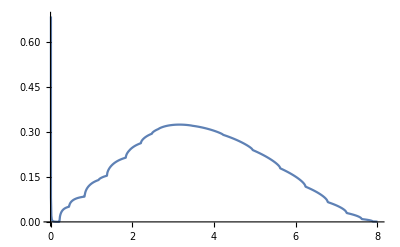

```mathematica
ListLinePlot[Table[{ω,-Im[SL[ω,0.0001,2.7,0,21][[2,2]]]},{ω,Range[0,8,0.01]}]]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].Lead[[ω*100+1]].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ,m].ρ[t,m].SR[ω,δ,t,ϵ,m].ρ[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ,m].ρ[t,m].SL[ω,δ,t,ϵ,m].ρ[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].ρ[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=tr[ω,δ,t,ϵ,m]=Abs[Tr[gdd[ω,δ,t,ϵ,m].ρ[t,m].grr[ω,δ,t,ϵ,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ,m].ρ[t,m].GNON[ω,δ,t,ϵ,m]]]
```

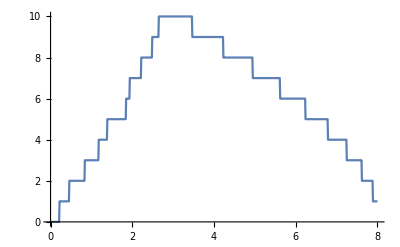

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,2.7,0,21]},{ω,Range[0,8,0.01]}]]
```

```mathematica
m[ω_,δ_,t_,ϵ_,m_,ϵ1_]:=Module[{Tin=T1[t,m],T=ρ[t,m],μ1=RandomInteger[{1,42}], μ2=RandomInteger[{1,42}], μ3=RandomInteger[{1,42}], μ4=RandomInteger[{1,42}],μ5=RandomInteger[{1,42}], μ6=RandomInteger[{1,42}], μ7=RandomInteger[{1,42}],μ8=RandomInteger[{1,42}], μ9=RandomInteger[{1,42}], μ10=RandomInteger[{1,42}], μ11=RandomInteger[{1,42}],μ12=RandomInteger[{1,42}], μ13=RandomInteger[{1,42}], μ14=RandomInteger[{1,42}](*, μ15=RandomInteger[{8,42}],μ16=RandomInteger[{8,42}]*),J=SL[ω,0.0001,2.7,0,21]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp8,imp8,imp,imp14,imp,imp3,imp9,imp4,imp11,imp4,imp7,imp2,imp13,imp4,imp13,imp4,imp7,imp1,imp7,imp4,imp14,imp7,imp4,imp12,imp8,imp11,imp9,imp11,imp12,imp6,imp4,imp11,imp4,imp,imp5,imp,imp9,imp,imp10,imp,imp,imp,imp10,imp6,imp14,imp2,imp6,imp11,imp8,imp1,imp6,imp14,imp5,imp2,imp12,imp,imp11,imp5,imp1,imp4,imp,imp3,imp8,imp10,imp10,imp13,imp,imp,imp13,imp7,imp3,imp12,imp1,imp9,imp13,imp4,imp13,imp14,imp10,imp3,imp2,imp6,imp1,imp5,imp9,imp2,imp9,imp4,imp2,imp12,imp,imp4,imp10,imp5,imp,imp14,imp6,imp7,imp1,imp,imp12,imp,imp3,imp5,imp8,imp3}]};
sl1= Module[{φ=SL[ω,0.0001,2.7,0,21]},Do[φ=Inverse[IdentityMatrix[2m]-lista[[1,ζ]].ConjugateTranspose[Tin].φ.Tin].lista[[1,ζ]],{ζ,1,100}]; φ=φ];Il1:=Inverse[IdentityMatrix[2m]-sl1.T.J.T].sl1;
Ir1:=Inverse[IdentityMatrix[2m]-J.T.sl1.T].J;gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= J.T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,2.7,0,21],tr[ω,0.0001,2.7,0,21],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
m[2.7,0.0001,2.7,0,21,0.5]
```

8.72572

```mathematica
Mean[Table[m[2.7,0.0001,2.7,0,21,0.5],2000]]//Timing
```

{704.574,8.55296}

```mathematica
Table[Mean[Table[m[ω,0.0001,2.7,0,21,0.5],2000]],{ω,Range[0,8,0.01]}]
```

```mathematica
RandomSample[Join[Flatten[Table[RandomSample[{imp1,imp2,imp3,imp4,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],6]],Table[imp,16]]]
```

{imp8,imp8,imp,imp14,imp,imp3,imp9,imp4,imp11,imp4,imp7,imp2,imp13,imp4,imp13,imp4,imp7,imp1,imp7,imp4,imp14,imp7,imp4,imp12,imp8,imp11,imp9,imp11,imp12,imp6,imp4,imp11,imp4,imp,imp5,imp,imp9,imp,imp10,imp,imp,imp,imp10,imp6,imp14,imp2,imp6,imp11,imp8,imp1,imp6,imp14,imp5,imp2,imp12,imp,imp11,imp5,imp1,imp4,imp,imp3,imp8,imp10,imp10,imp13,imp,imp,imp13,imp7,imp3,imp12,imp1,imp9,imp13,imp4,imp13,imp14,imp10,imp3,imp2,imp6,imp1,imp5,imp9,imp2,imp9,imp4,imp2,imp12,imp,imp4,imp10,imp5,imp,imp14,imp6,imp7,imp1,imp,imp12,imp,imp3,imp5,imp8,imp3}